# Seminarska naloga

## Zbirka nalog iz mature

Matematika (2015)

Damijan Randl

Ljubljana

14/01/2020

## 1. Naloga

Primerjajte števili a in b ter v srednji stolpec vstavite simbole > , <  ali  =.

```mathematica
-7/2<5/2
-2/3>-5/2
-2 √3 > -3 √2
π > 3.14
E > 2.7
2015^2015>2015!
```

True

True

True

«3 more identical outputs»

Za primerjanje števil sem uporabil kar logične operatorje, ki kot rezultat vrnejo True ali False.

### 1.1.)

Vpiši v tabelo:

```mathematica
TableForm[{{-7/2, "<", 5/2} , {-2/3, ">", -5/2}, {-2 √3, ">", -3 √2}, {π, ">", 3.14}, {"e", ">", 2.7}, {"2015^2015",">","2015!"}}, TableHeadings->{{},{"števila a","logicna vrednost" , "število b"}}]
```

| števila a | logicna vrednost | število b
 | -7/2 | < | 5/2
 | -2/3 | > | -5/2
 | -2 √3 | > | -3 √2
 | π | > | 3.14
 | e | > | 2.7
 | 2015^2015 | > | 2015!

Za osnovno tabelo uporabljamo izraz TableForm, ki nam iz danih podatkov v zavitih oklepajih izdela tabelo. Ker pa mi je lepši način z robovi, sem uporabil tudi funkcijo Grid, ki naredi in vrne sledečo obliko. (Mathematica sama ponudi tudi ukaze za stil in glavo tabele oz. mreže)

```mathematica
ReplacePart[Grid[{{-7/2,"<",5/2},{-2/3,">",-5/2},{-2 √3,">",-3 √2},{π,">",3.14},{"e",">",2.7},{"\!\(\*SuperscriptBox[\(2015\), \(2015\)]\)",">","2015!"}},{Dividers->All,Spacings->{1.5,1.5}}],1->Prepend[First[Grid[{{-7/2,"<",5/2},{-2/3,">",-5/2},{-2 √3,">",-3 √2},{π,">",3.14},{"e",">",2.7},{"\!\(\*SuperscriptBox[\(2015\), \(2015\)]\)",">","2015!"}},{Dividers->All,Spacings->{1.5,1.5}}]],{"število a","","število b"}]]
```

število a |  | število b
-7/2 | < | 5/2
-2/3 | > | -5/2
-2 √3 | > | -3 √2
π | > | 3.14
e | > | 2.7
2015^2015 | > | 2015!

## 2. Naloga

Dani so vektorji:  a⃗=(4,-3,1), b⃗=(-2,5,3)in  c⃗=(x,2,4).

```mathematica
a⃗={4,-3,1}
b⃗ = {-2, 5, 3}
c⃗={x,2,4}
```

{4,-3,1}

{-2,5,3}

{x,2,4}

### 2.1.)

Izračunajte  2 a⃗+b⃗.

```mathematica
Simplify[2 a⃗+b⃗]
```

{6,-1,5}

Seštevanje vektorjev je praktično enako seštevanji števil. Uporabljajo se isti operatorji.

### 2.2.)

Izračunajte  a⃗·b⃗.

```mathematica
Simplify[ a⃗.b⃗]
```

-20

Za skalarni produkt lahko uporabimo piko (.) ali pa ukaz Dot.

### 2.3.)

Izračunajte dolžino vektorja  b⃗.

```mathematica
dolzina = Norm[b⃗]
```

√38

```mathematica
N[dolzina]
```

6.16441

Odgovor: Dolžina vektorja b⃗  je  √38 oz. približno 6.16.

## 3. Naloga

Dana je funkcija f(x) s predpisom f(x) = 2sin(x) - 1.

```mathematica
ClearAll[x, f]
f[x_] = 2*Sin[x]-1
```

-1+2 Sin[x]

### 3.1.)

V dani koordinatni sistem narišite graf funkcije f(x).

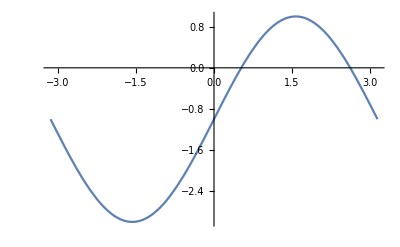

```mathematica
graf=Plot[f[x], {x, -π,π}]
```

### 3.2.)

Izračunaj odvod f(x).

```mathematica
odvod = D[f[x], x ]
```

2 Cos[x]

Odvod izračunamo z ukazom D(f) ali f’(x). Izgleda pa takole.

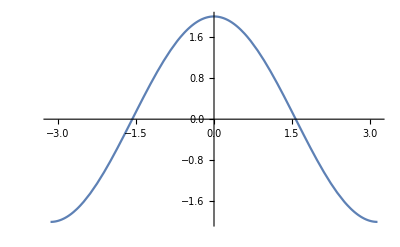

```mathematica
grafOdvoda=Plot[odvod, {x, -π, π}]
```

### 3.3.)

Izračunaj nedoločeni integral ∫f(x) dx.

```mathematica
integral = Integrate[f[x], x]
```

-x-2 Cos[x]

Za izračun integrala uporabljamo funkcijo Integrate. Graf pa izgleda sledeče.

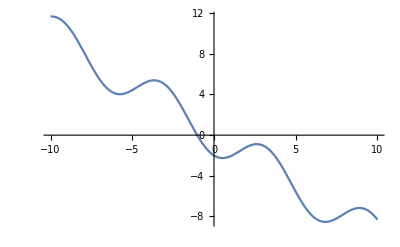

```mathematica
grafIntegrala=Plot[integral, {x, -10, 10}]
```

In še vsi trije na istem grafu:

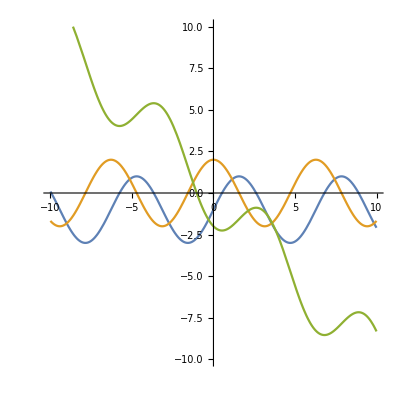

```mathematica
Plot[{f[x], odvod, integral}, {x, -10, 10}, AspectRatio->Automatic, PlotRange->{-10, 10}]
```

## 4. Naloga

Dano je kompleksno število z=√5-2 i. Izračunajte:

```mathematica
z = Sqrt[5]-2*I
```

-2 ⅈ+√5

### 4.1.)

z · z̄ =

```mathematica
Simplify[z * Conjugate[z]]
```

9

Conjugate je ukaz za konjugirano vrednost kompleksnega števila.

### 4.2.)

|z|=

```mathematica
Abs[z]
```

3

### 4.3.)

z^2+i^19=

```mathematica
FullSimplify[z^2 + I^19]
```

(1-ⅈ)-4 ⅈ √5

### 4.4.)

z^-1=

```mathematica
FullSimplify[ToRadicals[RootReduce[z^-1]]]
```

1/9 √(1+4 ⅈ √5)

Mathematica nima ukaza za racionalizacijo imenovalca?, in to je najboljši približek ki sem ga lahko dobil.

## 5. Naloga

Janez je dobil nalogo, da izračuna širino jezera med točkama A in B. Izmeril je |AC| = 255 m, |BC| = 232 m in δ = 56 °. Kolikšna je razdalja med točkama A in B? Rezultat zaokrožite na meter natančno.

```mathematica
Import["/Users/damijanrandl/Desktop/Screenshot 2020-01-18 at 14.09.14.png"]
```

-Graphics-

```mathematica
dolzinaAC = 255
dolzinaBC = 232
kot = 56°
```

255

232

56 °

Za računanje sem uporabil kosinusni izrek, ki se glasi √(b^2 +c^2 -2×b×c×cos(δ))

```mathematica
√(dolzinaAC^2+ dolzinaBC^2- 2*dolzinaAC*dolzinaBC* Cos[kot]) //N
```

229.533

Ker pa potrebujemo zgolj približen rezultat sem dobljeno številko zaokrožil na celo število.

```mathematica
NumberForm[229.53277687803376,3]
```

230.

Odgovor: Širina jezera med točko A in B je približno 230 m

## 6. Naloga

Pri katerih vrednostih realnega števila x leži graf funkcije f(x), ki je dana s predpisom f(x) = 2 x^2+4x-2, pod premico z enačbo y = - x + 1.

```mathematica
f[x_] := 2 x^2+4x-2
g[x_] := -x +1
```

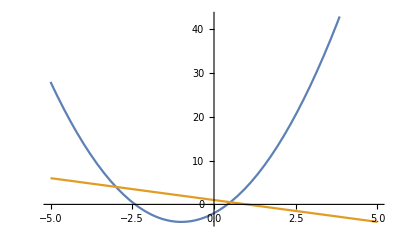

```mathematica
Plot[{f[x],g[x]}, {x, -5, 5}]
```

Za neenačbe uporabljamo ukaz Reduce.

```mathematica
Reduce[f[x]< g[x], x]
```

-3<x<1/2

Odgovor: Graf funkcije f(x) leži pod premico pri vrednostih: x ∈(-3, 1/2)

## 7.Naloga

Eksponentna funkcija f(x) ima predpis f(x)= 3^x-2/3.

```mathematica
f[x_] := 3^x-2/3
```

### 7.1)

Natančnno izračunajte neznani koordinati točke A(-3,y) in  B(x,25/3) na grafu funkcije f(x).

```mathematica
f[-3]
```

-17/27

Za izračun točke x sem uporabil ukaz SolveAlways. Opozori nas, da je možnost, da izpusti določene rešitve. A v tem primeru zadošča pravilni rešitvi.

```mathematica
SolveAlways[25/3==3^x-2/3, x]
```

SolveAlways::ifun: Inverse functions are being used by SolveAlways, so some solutions may not be found; use Reduce for complete solution information.

{{x→2}}

Odgovor: Dobimo točki na grafu: A (-3, -17/27)  in B (2, 25/3).

### 7.2)

Graf funkcije f(x) ima vodoravno asimptoto. Zapišite njeno enačbo.

```mathematica
Asimptota = Limit[f[x], x-> -Infinity]
```

-2/3

Odgovor: Enačba asimptote je y = -2/3.

Na grafu je prikazana asimptota funkcije f(x).

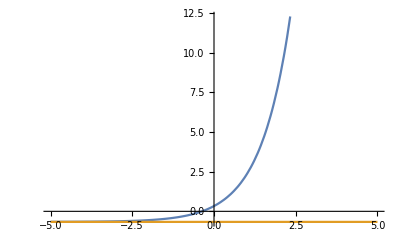

```mathematica
Plot[{f[x], Asimptota}, {x, -5, 5}]
```

## 8. Naloga

Parabola ima enačbo y=-x^2+4.

```mathematica
ClearAll[odvod]
f[x_]:= -x^2+4
```

### 8.1.)

V točki A(1, 3) položimo tangento na parabolo. Zapišite enačbo tangente.

```mathematica
odvod = D[f[x], x] /. x->1
tangenta= f'[x0](x-x0)+f[x0] /. x0 ->1
```

-2

3-2 (-1+x)

```mathematica
Simplify[tangenta]
```

5-2 x

Odgovor: enačba tangente je y = - 2x + 5. 
Graf pa prikazuje “gibanje” tangente na funkciji f(x) v odvistnosti od točke x0.

```mathematica
Manipulate[Plot[{f[x],f'[x0](x-x0)+f[x0] }, {x, -5, 5}, PlotRange -> {-10, 10}, Epilog -> {PointSize[Large] ,{Point[{x0, f[x0]}]}}], {{x0,1}, -4, 4}]
```

## 9. Naloga

Izračunaj limite:

Limite računamo z ukazom Limit, ki sprejme dva argumenta: v prvi del napičemo funkcijo, katere limito iščemo, v drugem delu pa določimo vrednost proti kateri teče x.

### 9.1.)

lim_(x→7) (x^2-49)/(x^2-2x-35)

```mathematica
f[x_]:=  (x^2-49)/(x^2-2x-35)
Limit[f[x], x->7]
```

7/6

Odgovor: Limita (x^2-49)/(x^2-2x-35) ko gre x proti 7 je 7/6.

### 9.2.)

lim_(x→0) sin3x/(5x)

```mathematica
f[x_]:=  Sin[3x]/(5x)
Limit[f[x], x->0]
```

3/5

Odgovor: Limita sin3x/(5x) ko gre x proti 7 je 3/5.

### 9.3.)

lim_(x→2) (√x-√2)/(x-2)

```mathematica
f[x_]:=  (√x-√2)/(x-2)
Limit[f[x], x->2]
```

1/(2 √2)

Odgovor: Limita (√x-√2)/(x-2) ko gre x proti 7 je 1/(2 √2) oz. (√2)/4 z racionalizacijo.

## 10. Naloga

Dana je racionalna funkcija f(x) = (x - 1)/(x + 1).

```mathematica
f[x_]:=(x-1)/(x+1)
```

### 10.1.)

V dani koordinatni sistem narišite krivuljo y = f(x). Zapišite predpis inverzne funkcije f^-1 in definicijsko območje funkcije f^-1.

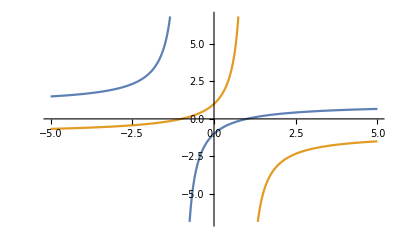

```mathematica
graf=Plot[{f[x], inverz[x]},{x, -5, 5}]
```

Narisana sta grafa funkcije f(x) in njenega inverza. Inverz izračunamo s pomočjo ukaza InverseFunction.

```mathematica
inverz = InverseFunction[f]
```

(-1-#1)/(-1+#1)&

Izraz, ki ga mathematica vrne je ekvivalenten izrazu (- 1 - 1)/(- 1 + 1).

Definicijsko območje inverzne funkcije je D_(f^-1) = ℝ - {1}.

```mathematica
DefinicijskoObmočje = FunctionDomain[inverz[x], x]
```

x<1||x>1

### 10.2.)

Naj premica y = 8x + n seka krivuljo y = f(x). Dokažite, da abcisi presečišča zadoščata enačbi 8 x^2 + (n + 7)x + n + 1 = 0.

```mathematica
ClearAll[g]
```

Najprej definiramo novo funkcijo premice.

```mathematica
g[x_, n_]:= 8x+n
```

Enačimo f(x) in g(x) in preverimo če sovpada z zgornjo enačbo.

```mathematica
Solve[g[x,n]==f[x],x]==Solve[8 x^2+(n+7)x+n+1==0,x]
```

True

Odgovor: Abcisi presešišča zadoščata enačbi 8 x^2 + (n + 7) x + n + 1 = 0

### 10.3.)

Izračunajte, za katere vrednosti parametra n je premica y = 8x + n tangenta na krivuljo y = f(x).

```mathematica
odvod = Simplify[D[f[x], x]]
```

2/(1+x)^2

Najprej enačimo odvod f’(x) z smernim koeficientom funkcije g(x).

```mathematica
dotikalisca= x/.Solve[odvod==8, x]
```

{-3/2,-1/2}

Dobimo abcisi dotikališč in sicer x_1 = - 3/2, x_2 = - 1/2

```mathematica
zacetnaVrednost1 = Simplify[Solve[8 x^2+(n+7)x+n+1==0, n]]/.x->dotikalisca
```

{{n→{17,1}}}

Izračunamo še začetno vrednost (n), tako, da abcisi dotikališč vstavimo v zgornjo enačbo. Dobimo dve rešitvi: n_1 = 17, n_2 = 1

```mathematica
Manipulate[Plot[{g[x, n], f[x]}, {x, -5, 5}, PlotRange->{-5, 10}, AspectRatio->Automatic], {n, 1, 17}]
```